```mathematica
Quit[];
```

## Mojo FPGA

```mathematica
<<JLink`;
```

```mathematica
JLink`AddToClassPath@FileNameJoin@{NotebookDirectory[],"java"};
Quiet@JLink`ReleaseJavaObject@port;
Quiet@JLink`ReleaseJavaObject@loader;
port=JLink`JavaNew["com.embeddedmicro.mojo.RegisterInterface"];
loader=JLink`JavaNew["com.embeddedmicro.mojo.MojoLoader"];
```

```mathematica
ClearAll[MojoRead];
MojoRead[port_,addr_Integer,n_Integer:1,increment:True|False:False]:=Module[{data=JLink`JavaNew["[I",{n}]},
port@read[addr,increment,data];
First@{JLink`JavaObjectToExpression@#,JLink`ReleaseJavaObject@#}&@data
];
ClearAll[MojoWrite];
MojoWrite[port_,addr_Integer,data_Integer]:=port@write[addr,data];
MojoData=Function[x,If[#>32768,#-65536,#]&/@QuotientRemainder[x,65536]];
```

```mathematica
port@disconnect[];
```

```mathematica
loader@sendBin["COM4",FileNameJoin@{NotebookDirectory[],"work\\planAhead\\dds_rom_mixer_filter_spi\\dds_rom_mixer_filter_spi.runs\\impl_1\\mojo_top_0.bin"},False,False]
```

```mathematica
port@connect["COM4"];
```

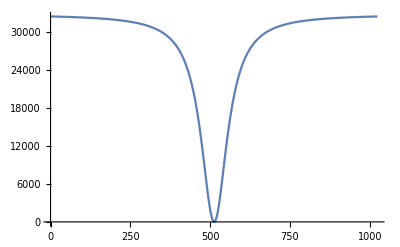

```mathematica
f[x_]:=x^2/(x^2+1);
g=f[a+b t+c Sin[ω t]]/.{a->0,b->1,c->0.,ω->2π 10};
ListLinePlot@Floor[32765.5Table[g,{t,-10.23,10.24,0.02}]]
```

```mathematica
wave=Floor[32767.5+32767.5Sin[2π Range[1024]/4096.]];
MojoWrite[port,1,#]&/@wave;
wave=Floor[255Table[g,{t,-10.23,10.24,0.02}]];
MojoWrite[port,4,1024+Length@wave-1];
MojoWrite[port,4,#]&/@wave;
```

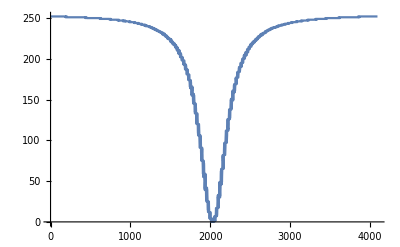
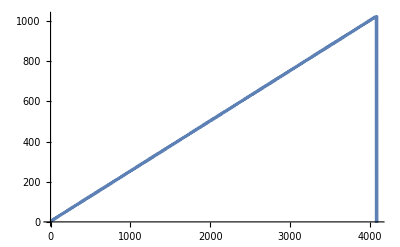

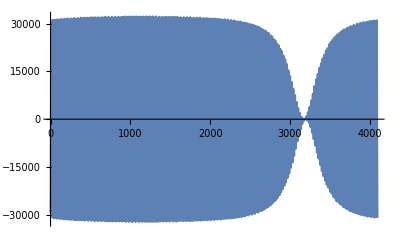

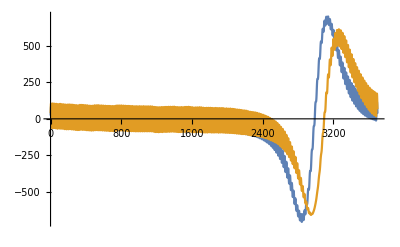

```mathematica
MojoWrite[port,2,64];
MojoWrite[port,3,200*256+0*65536];
MojoWrite[port,0,0];
MojoWrite[port,0,1+16*0+256*0+4096*2];
MojoWrite[port,1,0];
ListLinePlot/@Transpose[MojoData/@MojoRead[port,0,4096]]
MojoWrite[port,5,10];
MojoWrite[port,0,1+16*0+256*4+4096*3];
data=Transpose[MojoData/@MojoRead[port,0,4096]];
ListLinePlot[data⟦1⟧]
ListLinePlot[{LowpassFilter[data⟦1⟧,0.01],data⟦2⟧}⟦All,200;;-200⟧,PlotRange->Full]
```

```mathematica
MojoWrite[port,0,0];
MojoWrite[port,6,16^^28*65536+1];
MojoWrite[port,6,16^^20*65536+3];
MojoWrite[port,6,16^^38*65536+1];
MojoWrite[port,6,23*65536+32768];
MojoWrite[port,6,23*65536+32768+10000];
```

```mathematica
MojoWrite[port,6,16*65536+32768+0];
```

```mathematica
MojoWrite[port,6,17*65536+32768+0];
```

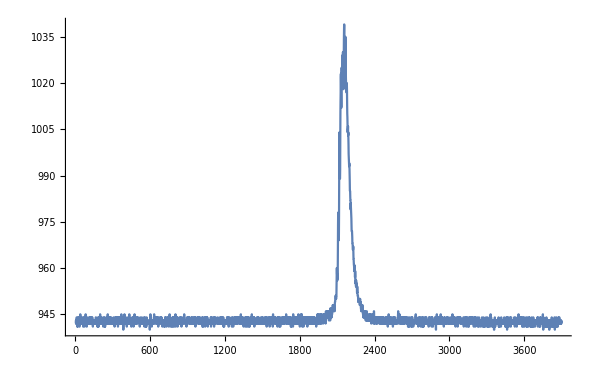

```mathematica
MojoWrite[port,2,10*256+(4*4096)*65536];
MojoWrite[port,0,64*65536+5];
Pause[0.1];
ListLinePlot[MojoRead[port,0,4096]⟦100;;-100⟧,PlotRange->Full]
```

```mathematica
MojoWrite[port,2,60*256+(4*4096+0)*65536];
MojoWrite[port,3,64+(2*4096)*65536];
MojoWrite[port,0,32*65536+6];
```

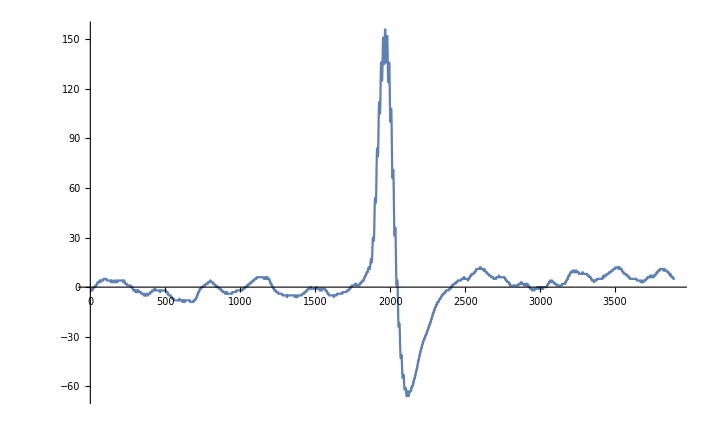

```mathematica
MojoWrite[port,2,60*256+(4*4096+0)*65536];
MojoWrite[port,3,64+(2*4096)*65536];
MojoWrite[port,5,10];
MojoWrite[port,7,945];
MojoWrite[port,0,16*65536+6];
Pause[0.1];
ListLinePlot[MojoRead[port,0,4096]⟦100;;-100⟧,PlotRange->Full]
```

```mathematica
MojoWrite[port,2,60*256+(3*4096+0)*65536];
MojoWrite[port,3,64+(1*4096)*65536];
MojoWrite[port,5,10];
MojoWrite[port,7,900];

MojoWrite[port,8,0];
MojoWrite[port,0,0];
MojoWrite[port,0,6];
MojoWrite[port,1,0];
```

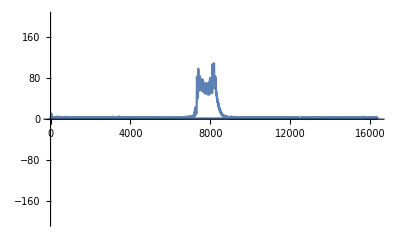

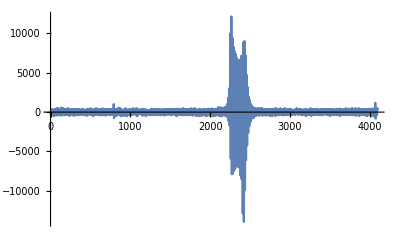
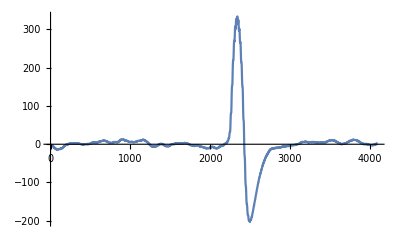

```mathematica
MojoWrite[port,0,6+16*5+256*5+4096*1];
Pause[0.1];
data=MojoData/@MojoRead[port,0,4096];
ListLinePlot[data,PlotRange->{-200,200}]
MojoWrite[port,0,6+16*5+256*4+4096*3];
Pause[0.1];
data=MojoData/@MojoRead[port,0,4096];
ListLinePlot[#,PlotRange->Full]&/@(dataᵀ)
```

```mathematica
MojoWrite[port,8,0];
Dynamic[MojoWrite[port,0,6+16*5+256*4+4096*1];
Pause[0.1];
data=MojoData/@MojoRead[port,0,4096];
ListLinePlot[data,PlotRange->{-200,200}],UpdateInterval->1]
```

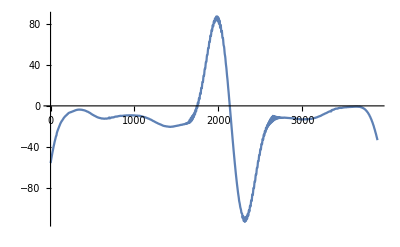

```mathematica
ListLinePlot[LowpassFilter[data⟦All,1⟧,0.005]⟦100;;-100⟧,PlotRange->Full]
```

```mathematica
MojoWrite[port,2,60*256+(2*4096+0)*65536];
Manipulate[MojoWrite[port,8,65536+Floor[x]];
MojoWrite[port,0,6+16*5+256*4+4096*5];
Pause[0.1];
data=MojoData/@MojoRead[port,0,4096];
Column[{ListLinePlot[data⟦All,1⟧,PlotRange->{0,200}],
ListLinePlot[data⟦All,2⟧,PlotRange->{-600,600}]}],{x,0,32767,100}]
```

```mathematica
MojoWrite[port,2,60*256+(2*4096+0)*65536];
Manipulate[MojoWrite[port,9,Floor[x]];
MojoWrite[port,0,7+16*5+256*4+4096*5];
Pause[0.1];
data=MojoData/@MojoRead[port,0,4096];
Column[{ListLinePlot[data⟦All,1⟧,PlotRange->{0,200}],
ListLinePlot[data⟦All,2⟧,PlotRange->{-600,600}]}],{x,0,32767,100}]
```

```mathematica
MojoWrite[port,9,65536*(-0)+7800];
MojoWrite[port,10,65536*100+10];
Dynamic[MojoWrite[port,0,7+16*5+256*6+4096*4];
Pause[0.1];
data=MojoData/@MojoRead[port,0,4096];
Column[{ListLinePlot[data⟦All,1⟧,PlotRange->{-400,400}],
ListLinePlot[data⟦All,2⟧,PlotRange->{0,15000}]}],UpdateInterval->1]
```

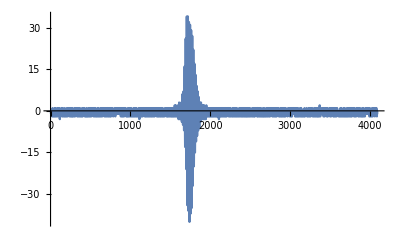

```mathematica
data=MojoRead[port,0,4096];
ListLinePlot[data,PlotRange->Full]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["data.csv",data];
```

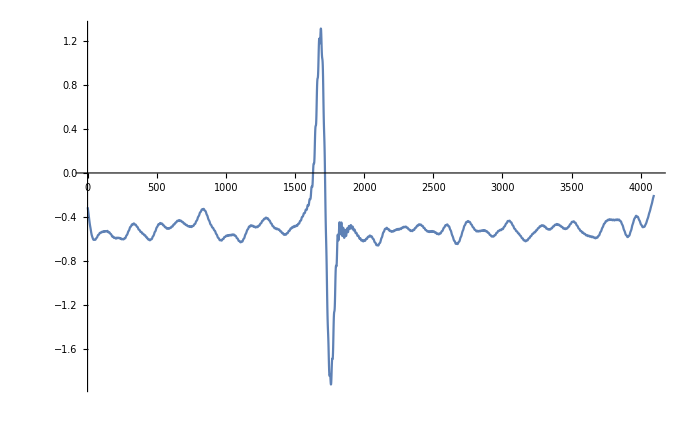

```mathematica
ListLinePlot[LowpassFilter[data,0.025],PlotRange->Full]
```

```mathematica
Dynamic[MojoWrite[port,0,64*65536+6];
Pause[0.1];
ListLinePlot[MojoRead[port,0,4096]⟦100;;-100⟧,PlotRange->Full],UpdateInterval->1]
```

```mathematica
MojoWrite[port,0,2];
```

```mathematica
MojoWrite[port,0,32*65536+2];
```

```mathematica
MojoWrite[port,0,32*65536+5];
```

```mathematica
MojoWrite[port,0,32*65536+6];
```

```mathematica
连续运行时mem改双口
```

```mathematica
MojoWrite[port,2,50*256+(1*4096)*65536];
MojoWrite[port,3,1*256+(2*4096)*65536];
MojoWrite[port,0,32*65536+2];
```

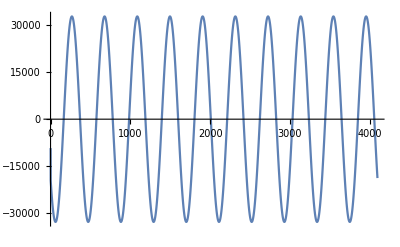

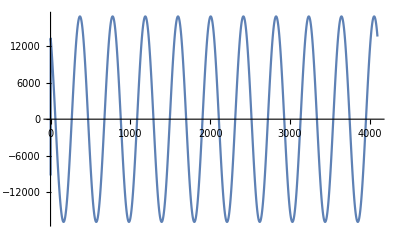

```mathematica
MojoWrite[port,2,10*256+0*65536];
MojoWrite[port,5,10];
MojoWrite[port,0,1*65536+3];
Pause[0.1];
ListLinePlot@MojoRead[port,0,4096]
MojoWrite[port,0,16*65536+3];
Pause[0.1];
ListLinePlot@MojoRead[port,0,4096]
```

```mathematica
MojoWrite[port,0,(1+32)*65536+3];
```

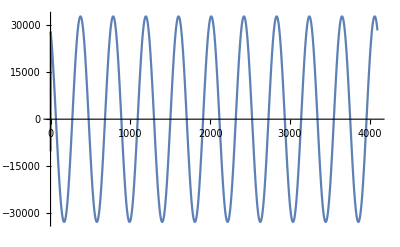

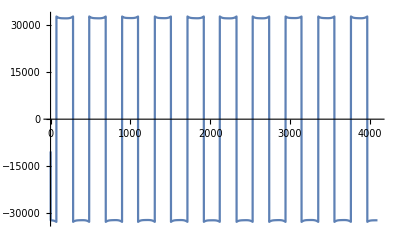

```mathematica
MojoWrite[port,2,10*256+0*65536];
MojoWrite[port,5,8];
MojoWrite[port,0,1*65536+3];
Pause[0.1];
ListLinePlot@MojoRead[port,0,4096]
MojoWrite[port,0,16*65536+3];
Pause[0.1];
ListLinePlot@MojoRead[port,0,4096]
```

## ADCTest

```mathematica
port@disconnect[];
```

```mathematica
port@connect["COM4"];
```

```mathematica
125MHz
```

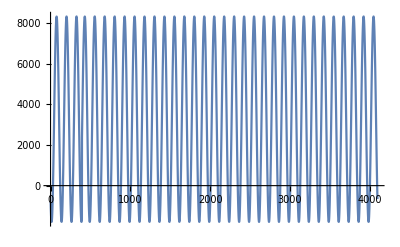

```mathematica
MojoWrite[port, 1, 3+3*65536];
MojoWrite[port, 0, 1];
 Pause[0.1]; 
MojoWrite[port, 0, 0]; 
ListLinePlot@MojoRead[port, 0, 4096]
```

```mathematica
100MHz
```

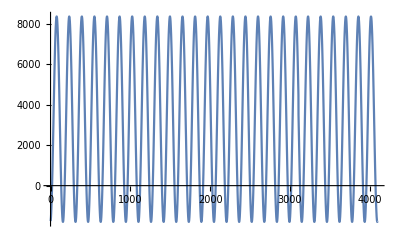

```mathematica
MojoWrite[port, 1, 3+3*65536];
MojoWrite[port, 0, 1];
 Pause[0.1]; 
MojoWrite[port, 0, 0]; 
ListLinePlot@MojoRead[port, 0, 4096]
```

```mathematica
Dynamic[Refresh[MojoWrite[port, 0, 1]; Pause[0.1]; 
  MojoWrite[port, 0, 0];ListLinePlot@MojoRead[port, 0, 4096]], 
  UpdateInterval ->1]
```